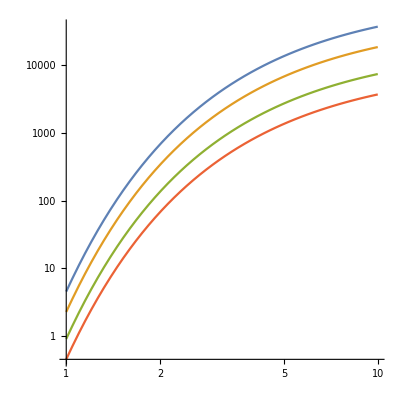

```mathematica
LogLogPlot[{10^5/1 ⅇ^(-10/x),10^5/2 ⅇ^(-10/x),10^5/5 ⅇ^(-10/x),10^5/10 ⅇ^(-10/x)},{x,1,10},AspectRatio->1]
```

```mathematica
Series[ⅇ^(-1/x),{x,0,4}]
```

ⅇ^(-1/x+O[x]^6)

```mathematica
D[ⅇ^(-1/x),x]
```

ⅇ^(-1/x)/x^2

```mathematica
With[{x=0},ⅇ^(-1/x)/x^2]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Indeterminate

General::munfl: Exp[-995.967] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-999.996] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

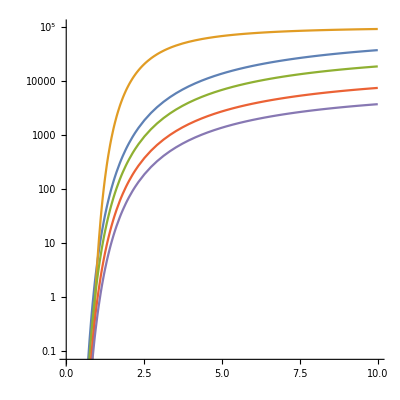

```mathematica
LogPlot[{10^5/1 ⅇ^(-10/x),10^5/1 ⅇ^(-10/x^2),10^5/2 ⅇ^(-10/x),10^5/5 ⅇ^(-10/x),10^5/10 ⅇ^(-10/x)},{x,.1,10},AspectRatio->1,PlotRange->{0.07,10^5}]
```

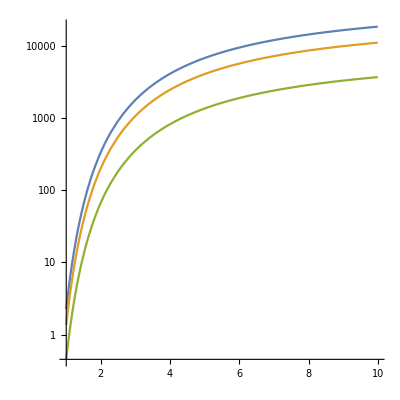

```mathematica
LogPlot[{10^5/1 ⅇ^(-10/x)-10^5/2 ⅇ^(-10/x),10^5/2 ⅇ^(-10/x)-10^5/5 ⅇ^(-10/x),10^5/5 ⅇ^(-10/x)-10^5/10 ⅇ^(-10/x)},{x,1,10},AspectRatio->1]
```